```mathematica
(*Time to do temperature stuff*)
```

```mathematica
$Assumptions={a∈Reals,u∈Reals,ub∈Reals,uh∈Reals,ub>uh,a>0,uh>0}
```

{a∈ℝ,u∈ℝ,ub∈ℝ,True,ub>0.2,a>0,True}

```mathematica
(*Strip Configurations*)
```

```mathematica
xavsy[yc_,yh_]:=Module[{xavsytb={},xavsytb2={}},
For[i=0,i<=3,i+=0.01,
yy=yc*10^i;
xa=Quiet[NIntegrate[Sqrt[((1+y^4)yc^6)/((y^4-yh^4)(y^6-yc^6))],{y,yc,yy}]];
AppendTo[xavsytb,{yy,xa}];
];
xavsytb2=Join[Reverse[xavsytb],Transpose[{xavsytb[[All,1]],-xavsytb[[All,2]]}]];
Return[xavsytb2];
];
```

```mathematica
xavsy1010=xavsy[1,1];
xavsy1210=xavsy[1.2,1];
xavsy4010=xavsy[4,1];
```

```mathematica
(*Insert SYM code*)
```

```mathematica
xvsu[uc_,uh_]:=Module[{xvsutb={},xvsutb2={}},
For[i=0,i<=3,i+=0.01,
uu=uc*10^i;
x=Quiet[NIntegrate[u^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,uu}]];
AppendTo[xvsutb,{uu,x}];
];
xvsutb2=Join[Reverse[xvsutb],Transpose[{xvsutb[[All,1]],-xvsutb[[All,2]]}]];
Return[xvsutb2];
]
```

```mathematica
xvsu1010=xvsu[1,1];
xvsu1210=xvsu[1.2,1];
xvsu4010=xvsu[4,1];
```

```mathematica
symxplt=ListLinePlot[{xvsu1010,xvsu1210,xvsu4010},ScalingFunctions->{"Log","SignedLog"},PlotRange->{{0,500},Automatic},Frame->True,FrameLabel->{"u_c","x"},PlotLegends->{"u_c=1","u_c=1.2","u_c=4"},FrameTicks->{{{-40,-10,-5,0,5,10,40},None},{Automatic,None}},PlotStyle->Dashed];
```

```mathematica
(*End SYM code*)
```

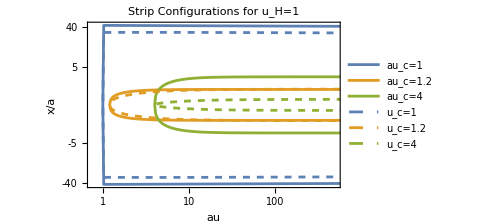

```mathematica
Show[{ListLinePlot[{xavsy1010,xavsy1210,xavsy4010},ScalingFunctions->{"Log","SignedLog"},PlotRange->{{0,500},Automatic},Frame->True,FrameLabel->{"au","x/a"},PlotLegends->{"au_c=1","au_c=1.2","au_c=4"},FrameTicks->{{{-40,-10,-5,0,5,10,40},None},{Automatic,None}}],symxplt},RotateLabel->False,PlotLabel->"Strip Configurations for u_H=1",ImageSize->Medium]
```

```mathematica
lavsyc[yh_]:=Module[{lavsyctb={}},
For[i=0,i<=2.5,i+=0.005,yc=2^i-0.93;
l=2*Quiet[NIntegrate[Sqrt[((1+y^4)yc^6)/((y^4-yh^4)(y^6-yc^6))],{y,yc,Infinity}]];
If[FreeQ[l,Complex],AppendTo[lavsyctb,{yc,l}]];
];
Return[lavsyctb];
];
```

```mathematica
lavsyc1=lavsyc[1];
lavsyc05=lavsyc[0.5];
lavsyc0=lavsyc[0];
```

```mathematica
(*Insert SYM code*)
```

```mathematica
lvsuc[uh_]:=Module[{lvsuctb={}},
For[i=0,i<=2.5,i+=0.005,uc=2^i-0.99;
l=2*Quiet[NIntegrate[u^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,Infinity}]];
If[FreeQ[l,Complex],AppendTo[lvsuctb,{uc,l}]];
];
Return[lvsuctb];
]
```

```mathematica
lvsuc1=lvsuc[1];
lvsuc05=lvsuc[0.5];
lvsuc0=lvsuc[0];
```

```mathematica
symlplt=ListLinePlot[{lvsuc0,lvsuc05,lvsuc1},Frame->True,PlotRange->{{0,3},{0,4}},FrameLabel->{"u_c","l"},PlotLegends->{"u_H=0","u_H=0.5","u_H=1"},PlotStyle->Dashed];(*End SYM code*)
```

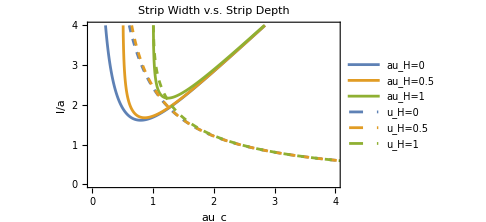

```mathematica
Show[{ListLinePlot[{lavsyc0,lavsyc05,lavsyc1},Frame->True,PlotRange->{{0,4},{0,4}},FrameLabel->{"au_c","l/a"},PlotLegends->{"au_H=0","au_H=0.5","au_H=1"}],symlplt},RotateLabel->False,PlotLabel->"Strip Width v.s. Strip Depth",ImageSize->Medium]
```

```mathematica
adiv=Integrate[u*Sqrt[(1+a^4 u^4)/(1-(uh/u)^4)],{u,uh,ub}]
```

(2 a^2 √((1+a^4 ub^4) (ub^4-uh^4))+(1+a^4 uh^4) Log[1+a^4 uh^4]-2 (1+a^4 uh^4) Log[√(1+a^4 ub^4)-a^2 √(ub^4-uh^4)])/(8 a^2)

```mathematica
FullSimplify[Series[adiv,{ub,Infinity,2}]]
```

(a^2 ub^4)/4+1/(8 a^2)(1-a^4 uh^4+Log[4]+a^4 uh^4 Log[4]+4 Log[a]+4 a^4 uh^4 Log[a]+4 Log[ub]+4 a^4 uh^4 Log[ub]-Log[1+a^4 uh^4]-a^4 uh^4 Log[1+a^4 uh^4])+O[1/ub]^3

```mathematica
delsfunc[yh_,alpha_,ycmax_]:=Module[{spvslatb={}},
For[yc=yh+0.0001,yc<=ycmax,yc+=0.001,
l=2*Quiet[NIntegrate[Sqrt[((1+y^4)yc^6)/((y^4-yh^4)(y^6-yc^6))],{y,yc,alpha}]];
sp=2*(Quiet[NIntegrate[y*Sqrt[(1+y^4)/((1-(yh/y)^4)(1-(yc/y)^6))],{y,yc,alpha}]]-(alpha^4/4+((1+yh^4)Log[alpha])/2));

AppendTo[spvslatb,{l,sp}];
];
Return[spvslatb];
];
```

```mathematica
lavsyca[yh_,alpha_]:=Module[{lavsyctb={}},
For[i=0,i<=2.5,i+=0.005,yc=2^i-0.93;
l=2*Quiet[NIntegrate[Sqrt[((1+y^4)yc^6)/((y^4-yh^4)(y^6-yc^6))],{y,yc,alpha}]];
If[FreeQ[l,Complex],AppendTo[lavsyctb,{yc,l}]];
];
Return[lavsyctb];
];
```

```mathematica
lavsyca07=lavsyca[0,7];
lavsyca057=lavsyca[0.15,7];
lavsyca17=lavsyca[0.2,7];
```

```mathematica
lavsyca07[[FirstPosition[lavsyca07,Min[lavsyca07[[All,2]]]]]]
lavsyca057[[FirstPosition[lavsyca057,Min[lavsyca057[[All,2]]]]]]
lavsyca17[[FirstPosition[lavsyca17,Min[lavsyca17[[All,2]]]]]]
```

{{0.805077,1.60343},{0.0734717,11.7388}}

{{0.805077,1.60396},{0.156735,9.27001}}

{{0.805077,1.60512},{0.206817,7.47779}}

```mathematica
ycmax0=0.8050773743041365;
lacrit0=1.6034274629607166;
ycmax05=0.8725009252216612;
lacrit05=1.6631819214676788;
ycmax1=1.2585874025214756;
lacrit1=2.130439106704549;
```

```mathematica
delsvsla07=delsfunc[0,7,0.8050773743041365];
delsvsla057=delsfunc[0.5,7,0.8725009252216612];
```

```mathematica
delsvsla17=delsfunc[1,7,1.2585874025214756];
```

```mathematica
(*alpha has to be really small to get what we expect here...*)
```

```mathematica
(*Insert SYM code*)
```

```mathematica
symdelsfunc[uh_,ub_]:=Module[{spvsltb={}},
For[uc=uh+0.0000001,uc<=3,uc+=0.001,
l=2*Quiet[NIntegrate[uc^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,ub}]];
sp=2*(Quiet[NIntegrate[u/Sqrt[(1-(uc/u)^6)(1-(uh/u)^4)],{u,uc,ub}]]-1/2 √(ub^4-uh^4));
AppendTo[spvsltb,{l,sp}];
];
Return[spvsltb];
];
```

```mathematica
symdelsvsl07=symdelsfunc[0,7];
symdelsvsl057=symdelsfunc[0.5,7];
symdelsvsl17=symdelsfunc[1,7];
```

```mathematica
symdelsplt=ListLinePlot[{symdelsvsl07,symdelsvsl057,symdelsvsl17},Frame->True,FrameLabel->{"l","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2S_A"},PlotLegends->{"u_H=0","u_H=0.5","u_H=1"},PlotStyle->Dashed];
```

```mathematica
(*End SYM code*)
```

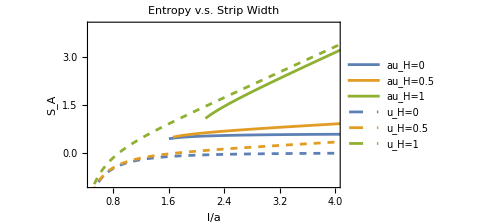

```mathematica
Show[{ListLinePlot[{delsvsla07,delsvsla057,delsvsla17},Frame->True,PlotRange->{{0.5,4},{-1,4}},FrameLabel->{"l/a","S_A"},PlotLegends->{"au_H=0","au_H=0.5","au_H=1"}],symdelsplt},RotateLabel->False,PlotLabel->"Entropy v.s. Strip Width",ImageSize->Medium]
```

```mathematica
(*fix above with constants*)
```

```mathematica
(*Begin Mutual Information*)
```

```mathematica
ucvslinterp[a_,yh_,ycmax_,alpha_]:=Module[{ucvsltb={}},
For[uc=yh/a+0.005,uc<=ycmax,uc+=0.005,
uh=yh/a;
l=2*Quiet[NIntegrate[Sqrt[((1+a^4 u^4)uc^6)/((u^4-uh^4)(u^6-uc^6))],{u,uc,alpha}]];
If[FreeQ[l,Complex],AppendTo[ucvsltb,{l,uc}]];
];
Clear[l];
Return[Interpolation[ucvsltb,InterpolationOrder->5]]
]
```

```mathematica
mutinffuncxl[a_,yh_,ycmax_,lacrit_,alpha_]:=Module[{mutinfvsxltb={}},
uh=yh/a;
firstucfunc=ucvslinterp[a,yh,ycmax,alpha];
lc=lacrit;
l=2*lc;
ucl=firstucfunc[l];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+a^4 u^4)/((1-(uh/u)^4)(1-(ucl/u)^6))],{u,ucl,alpha}]];
For[i=0,i≤1,i+=0.001,
x=lc+i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+a^4 u^4)/((1-(uh/u)^4)(1-(ucx/u)^6))],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+a^4 u^4)/((1-(uh/u)^4)(1-(uc2lx/u)^6))],{u,uc2lx,alpha}]];
mutinf=(2*splint - sp2lxint - spxint);
If[FreeQ[mutinf,Complex],AppendTo[mutinfvsxltb,{x/l,mutinf}]];
];
Return[mutinfvsxltb];
];
```

```mathematica
mutinfvsxl0507=Quiet[mutinffuncxl[0.5,0,ycmax0,lacrit0,7]];
mutinfvsxl050157=Quiet[mutinffuncxl[0.5,0.075,ycmax0,lacrit0,7]];
mutinfvsxl05027=Quiet[mutinffuncxl[0.5,0.1,ycmax0,lacrit0,7]];
```

```mathematica
(*Begin SYM code*)
```

```mathematica
symucvslinterp[uh_,ub_]:=Module[{ucvsltb={}},
For[uc=uh,uc<=3,uc+=0.001,
l=2*Quiet[NIntegrate[uc^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,ub}]];
If[FreeQ[l,Complex],AppendTo[ucvsltb,{l,uc}]];
];
Clear[l];
Return[Interpolation[ucvsltb]];
];
```

```mathematica
symmutinffuncxl[uh_,ub_,l_]:=Module[{mutinfvsxltb={}},
firstucfunc=symucvslinterp[uh,ub];
ucl=firstucfunc[l];
splint=2*Quiet[NIntegrate[u/Sqrt[(1-(ucl/u)^6)(1-(uh/u)^4)],{u,ucl,ub}]];
For[i=0,i<=1,i+=0.001,
x=i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
spxint=2*Quiet[NIntegrate[u/Sqrt[(1-(ucx/u)^6)(1-(uh/u)^4)],{u,ucx,ub}]];
sp2lxint=2*Quiet[NIntegrate[u/Sqrt[(1-(uc2lx/u)^6)(1-(uh/u)^4)],{u,uc2lx,ub}]];
mutinf=2*splint-sp2lxint-spxint;
If[FreeQ[mutinf,Complex],AppendTo[mutinfvsxltb,{x/l,mutinf}]];
];
Return[mutinfvsxltb];
];
```

```mathematica
symmutinf0201=Quiet[symmutinffuncxl[0,7,2*lacrit0]];
symmutinf015201=Quiet[symmutinffuncxl[0.15,7,2*lacrit0]];
symmutinf02201=Quiet[symmutinffuncxl[0.2,7,2*lacrit0]];
```

```mathematica
symmutinfplt=ListLinePlot[{symmutinf0201,symmutinf015201,symmutinf02201},Frame->True,FrameLabel->{"x/l",Subscript[Style["Ι",FontFamily->"Times"], AB]},
PlotLegends->{"u_H=0","u_H=0.15","u_H=0.2"},PlotStyle->Dashed];
```

```mathematica
(*End SYM code*)
```

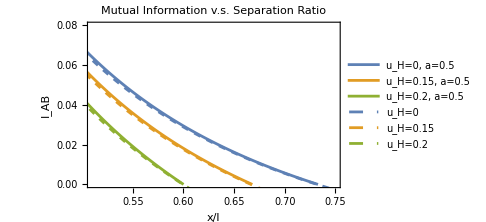

```mathematica
Show[{ListLinePlot[{mutinfvsxl0507,mutinfvsxl050157,mutinfvsxl05027},PlotRange->{{0.51,0.75},{0,0.08}},Frame->True,FrameLabel->{"x/l",Subscript[Style["Ι",FontFamily->"Times"], AB]},PlotLegends->{"u_H=0, a=0.5","u_H=0.15, a=0.5","u_H=0.2, a=0.5"}],symmutinfplt},PlotLabel->"Mutual Information v.s. Separation Ratio",RotateLabel->False, ImageSize->Medium]
```

```mathematica
mutinfvsxl107=Quiet[mutinffuncxl[1,0,ycmax0,lacrit0,7]];
mutinfvsxl10157=Quiet[mutinffuncxl[1,0.15,ycmax0,lacrit0,7]];
mutinfvsxl1027=Quiet[mutinffuncxl[1,0.2,ycmax0,lacrit0,7]];
```

```mathematica
symmutinf0202=Quiet[symmutinffuncxl[0,7,2*lacrit0]];
symmutinf015202=Quiet[symmutinffuncxl[0.15,7,2*lacrit0]];
```

```mathematica
symmutinf02202=Quiet[symmutinffuncxl[0.2,7,2*lacrit0]];
```

```mathematica
symmutinfplt2=ListLinePlot[{symmutinf0202,symmutinf015202,symmutinf02202},Frame->True,FrameLabel->{"x/l",Subscript[Style["Ι",FontFamily->"Times"], AB]},
PlotLegends->{"u_H=0","u_H=0.15","u_H=0.2"},PlotStyle->Dashed];
```

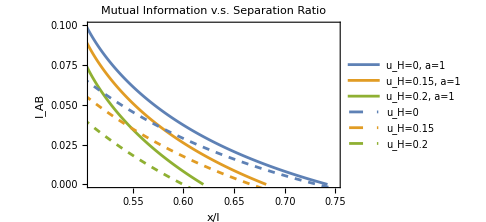

```mathematica
Show[{ListLinePlot[{mutinfvsxl107,mutinfvsxl10157,mutinfvsxl1027},Frame->True,FrameLabel->{"x/l",Subscript[Style["Ι",FontFamily->"Times"], AB]},PlotRange->{{0.51,0.75},{0,0.1}},PlotLegends->{"u_H=0, a=1","u_H=0.15, a=1","u_H=0.2, a=1"}],symmutinfplt2},PlotLabel->"Mutual Information v.s. Separation Ratio",RotateLabel->False,ImageSize->Medium]
```

```mathematica
(*holy shit it finally works after 1 million attempts*)
```

```mathematica
(*fucking hell, the green and orange crossover was just NIntegrate precision issues :( *)
```

```mathematica
testucfunc=symucvslinterp[0.2,7];
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

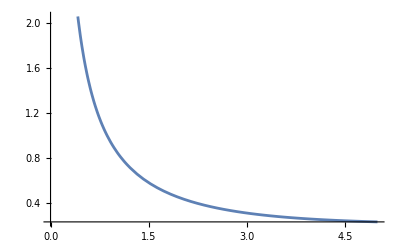

```mathematica
Plot[testucfunc[l],{l,0,5}]
```